7.20374×10^-7+2.42704×10^-13 x-6.58073×10^-20 x^2+1.16759×10^-26 x^3-1.10283×10^-33 x^4+4.15462×10^-41 x^5

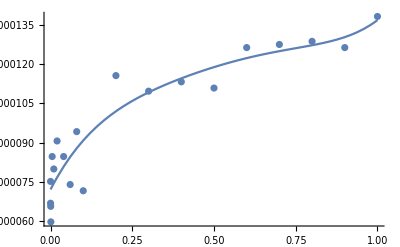

0.0000211462+6.03491×10^-12 x-5.65412×10^-18 x^2+1.76786×10^-24 x^3-2.1856×10^-31 x^4+9.28242×10^-39 x^5

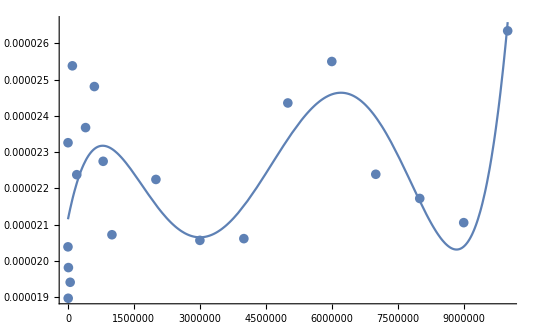

```mathematica
binaria=Fit[{{100,6.67572*10^-7},{1000,7.51019*10^-7},{5000,6.55651*10^-7},{10000,5.96046*10^-7},{50000,8.46386*10^-7},{100000,7.98702*10^-7},{200000,9.05991*10^-7},{400000,8.46386*10^-7},{600000,7.39098*10^-7},{800000,9.41753*10^-7},{1000000,7.15256*10^-7},{2000000,1.15633*10^-6},{3000000,1.09673*10^-6},{4000000,1.13249*10^-6},{5000000,1.10865*10^-6},{6000000,1.26362*10^-6},{7000000,1.27554*10^-6},{8000000,1.28746*10^-6},{9000000,1.26362*10^-6},{10000000,1.38283*10^-6}},{1,x,x^2,x^3,x^4,x^5},x]

puntosb=ListPlot[{{100,6.67572*10^-7},{1000,7.51019*10^-7},{5000,6.55651*10^-7},{10000,5.96046*10^-7},{50000,8.46386*10^-7},{100000,7.98702*10^-7},{200000,9.05991*10^-7},{400000,8.46386*10^-7},{600000,7.39098*10^-7},{800000,9.41753*10^-7},{1000000,7.15256*10^-7},{2000000,1.15633*10^-6},{3000000,1.09673*10^-6},{4000000,1.13249*10^-6},{5000000,1.10865*10^-6},{6000000,1.26362*10^-6},{7000000,1.27554*10^-6},{8000000,1.28746*10^-6},{9000000,1.26362*10^-6},{10000000,1.38283*10^-6}}]

g1=Plot[binaria,{x,0,10000000}]
Show[puntosb,g1,PlotRange->All]

binariahilos=Fit[{{100,2.03848*10^-5},{1000,2.32577*10^-5},{5000,1.89662*10^-5},{10000,1.98126*10^-5},{50000,1.94073*10^-5},{100000,2.53797*10^-5},{200000,2.23756*10^-5},{400000,2.3675*10^-5},{600000,2.48075*10^-5},{800000,2.27451*10^-5},{1000000,2.07186*10^-5},{2000000,2.22445*10^-5},{3000000,2.05636*10^-5},{4000000,2.06113*10^-5},{5000000,2.43545*10^-5},{6000000,2.54989*10^-5},{7000000,2.23875*10^-5},{8000000,2.17199*10^-5},{9000000,2.10524*10^-5},{10000000,2.63453*10^-5}},{1,x,x^2,x^3,x^4,x^5},x]

puntosbh=ListPlot[{{100,2.03848*10^-5},{1000,2.32577*10^-5},{5000,1.89662*10^-5},{10000,1.98126*10^-5},{50000,1.94073*10^-5},{100000,2.53797*10^-5},{200000,2.23756*10^-5},{400000,2.3675*10^-5},{600000,2.48075*10^-5},{800000,2.27451*10^-5},{1000000,2.07186*10^-5},{2000000,2.22445*10^-5},{3000000,2.05636*10^-5},{4000000,2.06113*10^-5},{5000000,2.43545*10^-5},{6000000,2.54989*10^-5},{7000000,2.23875*10^-5},{8000000,2.17199*10^-5},{9000000,2.10524*10^-5},{10000000,2.63453*10^-5}}]

g2=Plot[binariahilos,{x,0,10000000}]
Show[puntosbh,g2,PlotRange->All]
```